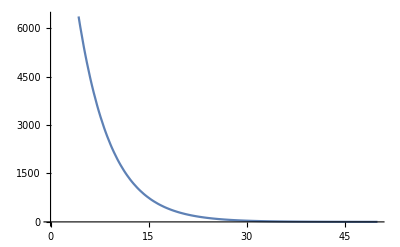

```mathematica
Plot[15000*E^(-t/5),{t, 0,50}]
```

# Q2.2 Mathematical Model and Questions

## 3.(a)

## h = 1

15000 ⅇ^(-t/5)

-3000 ⅇ^(-t/5)

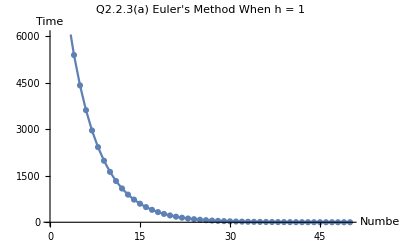

{{0,3000},{0,3000/ⅇ^(1/5)},{0,3000/ⅇ^(2/5)},{0,3000/ⅇ^(3/5)},{0,3000/ⅇ^(4/5)},{0,3000/ⅇ},{0,3000/ⅇ^(6/5)},{0,3000/ⅇ^(7/5)},{0,3000/ⅇ^(8/5)},{0,3000/ⅇ^(9/5)},{0,3000/ⅇ^2},{0,3000/ⅇ^(11/5)},{0,3000/ⅇ^(12/5)},{0,3000/ⅇ^(13/5)},{0,3000/ⅇ^(14/5)},{0,3000/ⅇ^3},{0,3000/ⅇ^(16/5)},{0,3000/ⅇ^(17/5)},{0,3000/ⅇ^(18/5)},{0,3000/ⅇ^(19/5)},{0,3000/ⅇ^4},{0,3000/ⅇ^(21/5)},{0,3000/ⅇ^(22/5)},{0,3000/ⅇ^(23/5)},{0,3000/ⅇ^(24/5)},{0,3000/ⅇ^5},{0,3000/ⅇ^(26/5)},{0,3000/ⅇ^(27/5)},{0,3000/ⅇ^(28/5)},{0,3000/ⅇ^(29/5)},{0,3000/ⅇ^6},{0,3000/ⅇ^(31/5)},{0,3000/ⅇ^(32/5)},{0,3000/ⅇ^(33/5)},{0,3000/ⅇ^(34/5)},{0,3000/ⅇ^7},{0,3000/ⅇ^(36/5)},{0,3000/ⅇ^(37/5)},{0,3000/ⅇ^(38/5)},{0,3000/ⅇ^(39/5)},{0,3000/ⅇ^8},{0,3000/ⅇ^(41/5)},{0,3000/ⅇ^(42/5)},{0,3000/ⅇ^(43/5)},{0,3000/ⅇ^(44/5)},{0,3000/ⅇ^9},{0,3000/ⅇ^(46/5)},{0,3000/ⅇ^(47/5)},{0,3000/ⅇ^(48/5)},{0,3000/ⅇ^(49/5)},{0,3000/ⅇ^10}}

```mathematica
h=1;
t0=0;
y = 15000*E^(-t/5)
Z=D[15000*E^(-t/5),t]
A = y + h *Z;
g1 = Show[
ListLinePlot[Table[{t,A},{t,0,50,1}]] ,      ListPlot[Table[{t,A},{t,0,50,1}]]       , AxesLabel-> {"Number","Time"}    ,PlotLabel-> "Q2.2.3(a) Euler's Method When h = 1"]
Error = Table[{t, y}, {t,0,50,1}]          -       Table[{t,A},{t,0,50,1}]
```

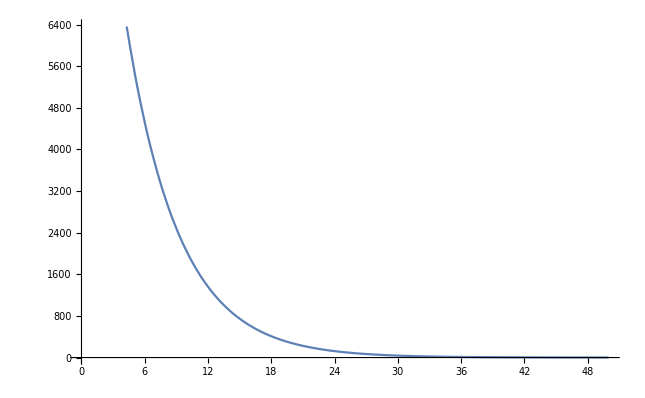
15000 ⅇ^(-t/5) -Graphics-

```mathematica
15000 ⅇ^(-t/5)Plot[15000*E^(-t/5),{t, 0,50}]
```

## h = 0.1

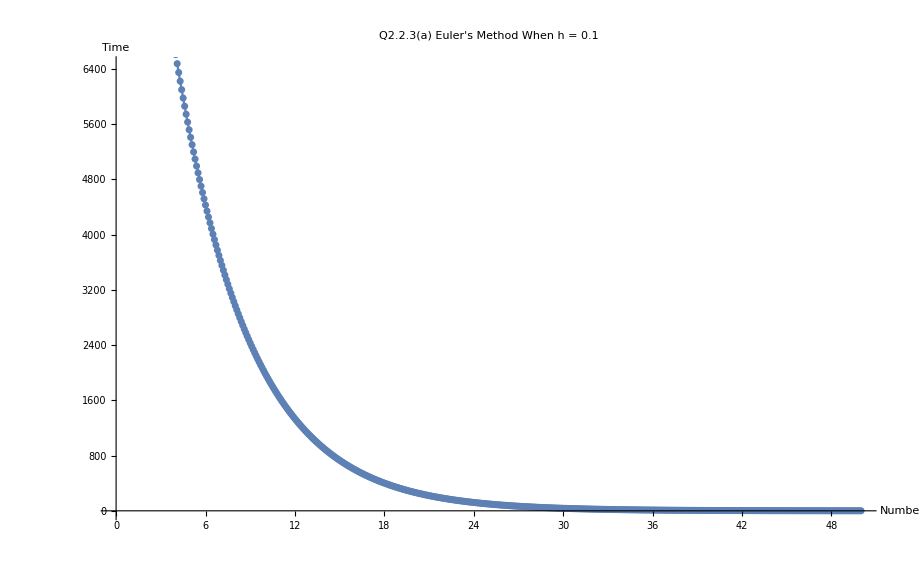

{{0.,300.},{0.,294.06},{0.,288.237},{0.,282.529},{0.,276.935},{0.,271.451},{0.,266.076},{0.,260.807},{0.,255.643},{0.,250.581},{0.,245.619},{0.,240.756},{0.,235.988},{0.,231.315},{0.,226.735},{0.,222.245},{0.,217.845},{0.,213.531},{0.,209.303},{0.,205.158},{0.,201.096},{0.,197.114},{0.,193.211},{0.,189.385},{0.,185.635},{0.,181.959},{0.,178.356},{0.,174.824},{0.,171.363},{0.,167.97},{0.,164.643},{0.,161.383},{0.,158.188},{0.,155.055},{0.,151.985},{0.,148.976},{0.,146.026},{0.,143.134},{0.,140.3},{0.,137.522},{0.,134.799},{0.,132.129},{0.,129.513},{0.,126.949},{0.,124.435},{0.,121.971},{0.,119.556},{0.,117.188},{0.,114.868},{0.,112.593},{0.,110.364},{0.,108.178},{0.,106.036},{0.,103.937},{0.,101.879},{0.,99.8613},{0.,97.8839},{0.,95.9457},{0.,94.0459},{0.,92.1836},{0.,90.3583},{0.,88.5691},{0.,86.8153},{0.,85.0962},{0.,83.4112},{0.,81.7595},{0.,80.1406},{0.,78.5537},{0.,76.9982},{0.,75.4736},{0.,73.9791},{0.,72.5142},{0.,71.0783},{0.,69.6709},{0.,68.2913},{0.,66.939},{0.,65.6136},{0.,64.3143},{0.,63.0408},{0.,61.7925},{0.,60.569},{0.,59.3696},{0.,58.194},{0.,57.0417},{0.,55.9122},{0.,54.8051},{0.,53.7198},{0.,52.6561},{0.,51.6135},{0.,50.5914},{0.,49.5897},{0.,48.6077},{0.,47.6452},{0.,46.7018},{0.,45.777},{0.,44.8706},{0.,43.9821},{0.,43.1112},{0.,42.2575},{0.,41.4208},{0.,40.6006},{0.,39.7966},{0.,39.0086},{0.,38.2362},{0.,37.4791},{0.,36.7369},{0.,36.0095},{0.,35.2965},{0.,34.5975},{0.,33.9125},{0.,33.2409},{0.,32.5827},{0.,31.9376},{0.,31.3051},{0.,30.6853},{0.,30.0777},{0.,29.4821},{0.,28.8983},{0.,28.3261},{0.,27.7652},{0.,27.2154},{0.,26.6765},{0.,26.1483},{0.,25.6305},{0.,25.123},{0.,24.6255},{0.,24.1379},{0.,23.6599},{0.,23.1914},{0.,22.7322},{0.,22.2821},{0.,21.8409},{0.,21.4084},{0.,20.9845},{0.,20.5689},{0.,20.1617},{0.,19.7624},{0.,19.3711},{0.,18.9875},{0.,18.6116},{0.,18.243},{0.,17.8818},{0.,17.5277},{0.,17.1806},{0.,16.8404},{0.,16.507},{0.,16.1801},{0.,15.8597},{0.,15.5457},{0.,15.2379},{0.,14.9361},{0.,14.6404},{0.,14.3505},{0.,14.0663},{0.,13.7878},{0.,13.5148},{0.,13.2472},{0.,12.9848},{0.,12.7277},{0.,12.4757},{0.,12.2287},{0.,11.9865},{0.,11.7492},{0.,11.5165},{0.,11.2885},{0.,11.065},{0.,10.8458},{0.,10.6311},{0.,10.4206},{0.,10.2142},{0.,10.012},{0.,9.81373},{0.,9.61941},{0.,9.42893},{0.,9.24222},{0.,9.05922},{0.,8.87983},{0.,8.704},{0.,8.53165},{0.,8.36271},{0.,8.19712},{0.,8.0348},{0.,7.8757},{0.,7.71975},{0.,7.56689},{0.,7.41706},{0.,7.27019},{0.,7.12623},{0.,6.98512},{0.,6.84681},{0.,6.71123},{0.,6.57834},{0.,6.44808},{0.,6.3204},{0.,6.19525},{0.,6.07257},{0.,5.95233},{0.,5.83446},{0.,5.71893},{0.,5.60569},{0.,5.49469},{0.,5.38589},{0.,5.27924},{0.,5.17471},{0.,5.07224},{0.,4.9718},{0.,4.87335},{0.,4.77686},{0.,4.68227},{0.,4.58955},{0.,4.49867},{0.,4.40959},{0.,4.32228},{0.,4.23669},{0.,4.1528},{0.,4.07057},{0.,3.98997},{0.,3.91096},{0.,3.83352},{0.,3.75761},{0.,3.6832},{0.,3.61027},{0.,3.53878},{0.,3.46871},{0.,3.40002},{0.,3.3327},{0.,3.26671},{0.,3.20202},{0.,3.13862},{0.,3.07647},{0.,3.01555},{0.,2.95584},{0.,2.89731},{0.,2.83994},{0.,2.7837},{0.,2.72858},{0.,2.67455},{0.,2.62159},{0.,2.56968},{0.,2.5188},{0.,2.46892},{0.,2.42004},{0.,2.37212},{0.,2.32515},{0.,2.2791},{0.,2.23397},{0.,2.18974},{0.,2.14638},{0.,2.10388},{0.,2.06222},{0.,2.02138},{0.,1.98136},{0.,1.94212},{0.,1.90367},{0.,1.86597},{0.,1.82902},{0.,1.79281},{0.,1.75731},{0.,1.72251},{0.,1.6884},{0.,1.65497},{0.,1.6222},{0.,1.59008},{0.,1.55859},{0.,1.52773},{0.,1.49748},{0.,1.46783},{0.,1.43876},{0.,1.41027},{0.,1.38235},{0.,1.35497},{0.,1.32814},{0.,1.30184},{0.,1.27607},{0.,1.2508},{0.,1.22603},{0.,1.20175},{0.,1.17796},{0.,1.15463},{0.,1.13177},{0.,1.10936},{0.,1.08739},{0.,1.06586},{0.,1.04476},{0.,1.02407},{0.,1.00379},{0.,0.983913},{0.,0.96443},{0.,0.945333},{0.,0.926615},{0.,0.908266},{0.,0.890282},{0.,0.872653},{0.,0.855373},{0.,0.838436},{0.,0.821833},{0.,0.80556},{0.,0.789609},{0.,0.773974},{0.,0.758648},{0.,0.743626},{0.,0.728901},{0.,0.714468},{0.,0.70032},{0.,0.686453},{0.,0.67286},{0.,0.659537},{0.,0.646477},{0.,0.633676},{0.,0.621128},{0.,0.608829},{0.,0.596774},{0.,0.584957},{0.,0.573374},{0.,0.56202},{0.,0.550891},{0.,0.539983},{0.,0.529291},{0.,0.51881},{0.,0.508537},{0.,0.498467},{0.,0.488597},{0.,0.478922},{0.,0.469439},{0.,0.460143},{0.,0.451032},{0.,0.442101},{0.,0.433347},{0.,0.424766},{0.,0.416355},{0.,0.40811},{0.,0.400029},{0.,0.392108},{0.,0.384344},{0.,0.376733},{0.,0.369274},{0.,0.361961},{0.,0.354794},{0.,0.347769},{0.,0.340882},{0.,0.334133},{0.,0.327516},{0.,0.321031},{0.,0.314674},{0.,0.308443},{0.,0.302336},{0.,0.296349},{0.,0.290481},{0.,0.284729},{0.,0.279091},{0.,0.273565},{0.,0.268148},{0.,0.262838},{0.,0.257633},{0.,0.252532},{0.,0.247531},{0.,0.24263},{0.,0.237826},{0.,0.233116},{0.,0.2285},{0.,0.223976},{0.,0.219541},{0.,0.215194},{0.,0.210932},{0.,0.206756},{0.,0.202662},{0.,0.198649},{0.,0.194715},{0.,0.19086},{0.,0.18708},{0.,0.183376},{0.,0.179745},{0.,0.176186},{0.,0.172697},{0.,0.169277},{0.,0.165925},{0.,0.16264},{0.,0.159419},{0.,0.156263},{0.,0.153168},{0.,0.150135},{0.,0.147163},{0.,0.144249},{0.,0.141392},{0.,0.138592},{0.,0.135848},{0.,0.133158},{0.,0.130521},{0.,0.127937},{0.,0.125404},{0.,0.12292},{0.,0.120487},{0.,0.118101},{0.,0.115762},{0.,0.11347},{0.,0.111223},{0.,0.109021},{0.,0.106862},{0.,0.104746},{0.,0.102672},{0.,0.100639},{0.,0.098646},{0.,0.0966927},{0.,0.094778},{0.,0.0929013},{0.,0.0910617},{0.,0.0892586},{0.,0.0874912},{0.,0.0857587},{0.,0.0840606},{0.,0.0823961},{0.,0.0807645},{0.,0.0791653},{0.,0.0775977},{0.,0.0760612},{0.,0.074555},{0.,0.0730788},{0.,0.0716317},{0.,0.0702133},{0.,0.068823},{0.,0.0674602},{0.,0.0661244},{0.,0.064815},{0.,0.0635316},{0.,0.0622736},{0.,0.0610405},{0.,0.0598318},{0.,0.0586471},{0.,0.0574858},{0.,0.0563475},{0.,0.0552317},{0.,0.0541381},{0.,0.0530661},{0.,0.0520153},{0.,0.0509853},{0.,0.0499757},{0.,0.0489862},{0.,0.0480162},{0.,0.0470654},{0.,0.0461334},{0.,0.0452199},{0.,0.0443245},{0.,0.0434468},{0.,0.0425865},{0.,0.0417432},{0.,0.0409167},{0.,0.0401065},{0.,0.0393123},{0.,0.0385339},{0.,0.0377709},{0.,0.0370229},{0.,0.0362898},{0.,0.0355713},{0.,0.0348669},{0.,0.0341765},{0.,0.0334997},{0.,0.0328364},{0.,0.0321862},{0.,0.0315489},{0.,0.0309242},{0.,0.0303118},{0.,0.0297116},{0.,0.0291233},{0.,0.0285466},{0.,0.0279813},{0.,0.0274273},{0.,0.0268842},{0.,0.0263518},{0.,0.02583},{0.,0.0253186},{0.,0.0248172},{0.,0.0243258},{0.,0.0238441},{0.,0.023372},{0.,0.0229092},{0.,0.0224555},{0.,0.0220109},{0.,0.0215751},{0.,0.0211478},{0.,0.0207291},{0.,0.0203186},{0.,0.0199163},{0.,0.0195219},{0.,0.0191354},{0.,0.0187565},{0.,0.018385},{0.,0.018021},{0.,0.0176642},{0.,0.0173144},{0.,0.0169715},{0.,0.0166355},{0.,0.0163061},{0.,0.0159832},{0.,0.0156667},{0.,0.0153565},{0.,0.0150524},{0.,0.0147543},{0.,0.0144622},{0.,0.0141758},{0.,0.0138951},{0.,0.01362}}

```mathematica
h=0.1;
t0=0;
y = 15000*E^(-t/5);
Z=D[15000*E^(-t/5),t];
A = y + h *Z;
g1 = Show[
ListLinePlot[Table[{t,A},{t,0,50,0.1}]] ,      ListPlot[Table[{t,A},{t,0,50,0.1}]]       , AxesLabel-> {"Number","Time"}    ,PlotLabel-> "Q2.2.3(a) Euler's Method When h = 0.1"]
Error = Table[{t, y}, {t,0,50,0.1}]          -       Table[{t,A},{t,0,50,0.1}]
```

### h=0.01

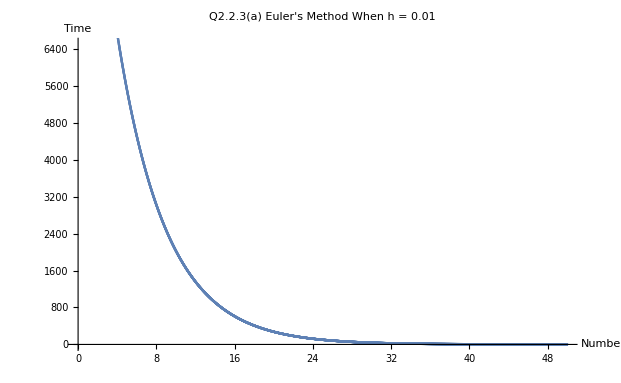

{{0.,30.},{0.,29.9401},{0.,29.8802},{0.,29.8205},{0.,29.761},{0.,29.7015},{0.,29.6422},{0.,29.5829},{0.,29.5238},{0.,29.4648},{0.,29.406},{0.,29.3472},{0.,29.2886},{0.,29.2301},{0.,29.1717},4971,{0.,0.00140067},{0.,0.00139787},{0.,0.00139508},{0.,0.00139229},{0.,0.00138951},{0.,0.00138674},{0.,0.00138397},{0.,0.0013812},{0.,0.00137844},{0.,0.00137569},{0.,0.00137294},{0.,0.00137019},{0.,0.00136746},{0.,0.00136472},{0.,0.001362}}
 |  |  |  |

```mathematica
h=0.01;
t0=0;
y = 15000*E^(-t/5);
Z=D[15000*E^(-t/5),t];
A = y + h *Z;
g2 = Show[
ListLinePlot[Table[{t,A},{t,0,50,0.01}]] ,      ListPlot[Table[{t,A},{t,0,50,0.01}]]       , AxesLabel-> {"Number","Time"}    ,PlotLabel-> "Q2.2.3(a) Euler's Method When h = 0.01"]
Error = Table[{t, y}, {t,0,50,0.01}]          -       Table[{t,A},{t,0,50,0.01}]
```

## Compare original function and Euler’s Method h = 1

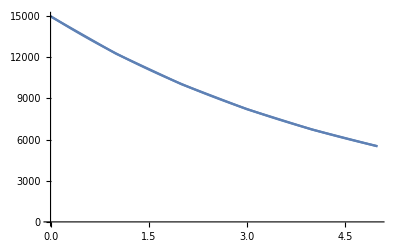

```mathematica
h=0.01;
t0=0;
y = 15000*E^(-t/5);
Z=D[15000*E^(-t/5),t];
A = y + h *Z;

Show[
    ListLinePlot[Table[{t,A},{t,0,5,1}]],       Plot[15000*E^(-t/5),{t, 0,5}] ]
```

## Assume Nb(0) = 1000, the graph of Nb

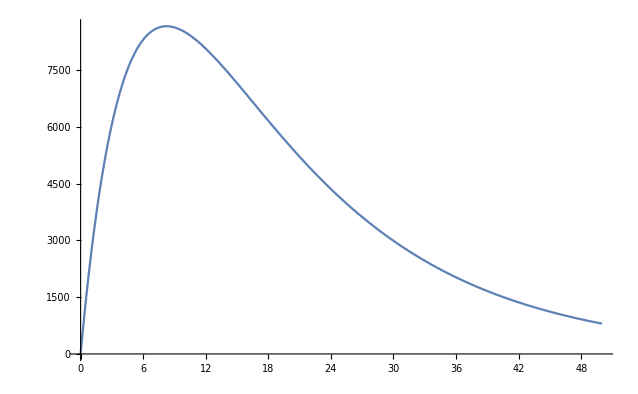

```mathematica
Plot[B = (3000/(1/15- 0.2))(E^(-0.2t)-E^(-1/15*t)), {t, 0, 50}]
```

## Assume Nc(0) = 0, the graph of Nc

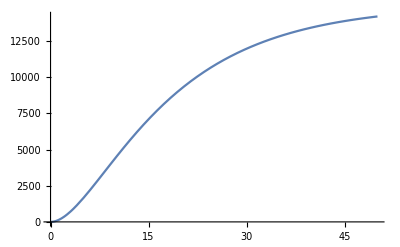

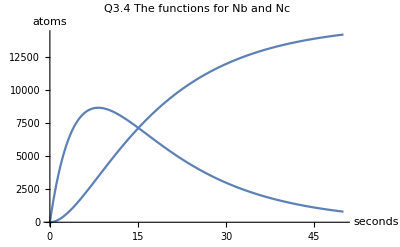

```mathematica
Plot[ 1000/(1/15-0.2)*(1-E^(-0.2t))+ 3000/(1/15 -0.2)*(E^(-1/15t) -1),  {t, 0,50}]
g3 = Show[
                  Plot[ 1000/(1/15-0.2)*(1-E^(-0.2t))+ 3000/(1/15 -0.2)*(E^(-1/15t) -1),  {t, 0,50}], Plot[B = (3000/(1/15- 0.2))(E^(-0.2t)-E^(-1/15*t)), {t, 0, 50}], AxesLabel-> {"seconds","atoms"}    ,PlotLabel-> "Q3.4 The functions for Nb and Nc" ]
```

# 5.

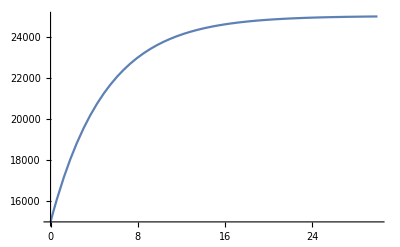

25000-10000 ⅇ^(-0.2 t)

15000 ⅇ^(-t/5)

-3000 ⅇ^(-t/5)

```mathematica
Plot[a, {t, 0,30}]
a = 25000-10000/(E^(0.2t))
```

# Q3.6 and 3.7

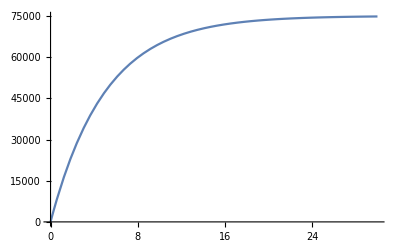

```mathematica
Plot[75000-75000E^(-0.2t), {t,0,30}]
```

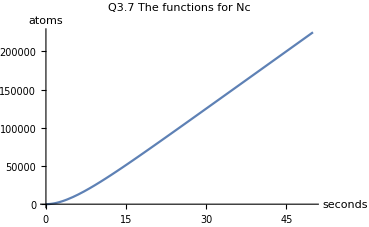

```mathematica
Plot[5000t+25000E^(-0.2t)-25000, {t, 0, 50} , AxesLabel-> {"seconds","atoms"}, PlotLabel-> "Q3.7 The functions for Nc"]
```

# Q3.6 and 3.7 Compare with Na and Nb

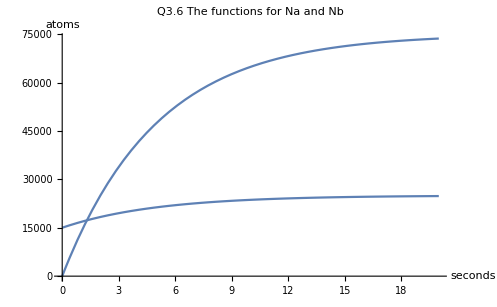

```mathematica
Show[Plot[75000-75000E^(-0.2t), {t,0,20}]     , Plot[25000-10000/(E^(0.2t)), {t, 0,20}]  ,AxesLabel-> {"seconds","atoms"}, PlotLabel-> "Q3.6 The functions for Na and Nb"]
```